{QL→520.813,ρ→0.862189,d→0.86253,ϕ→3.16971,t0→-0.0000337735}

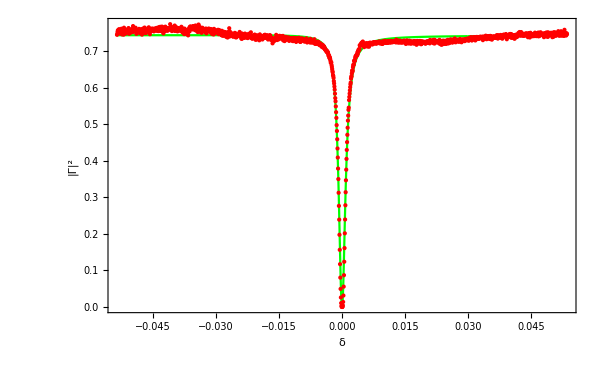

Q_0 -> 970.182

f_res[MHz] ->           9
2.33445 10

Q_L -> 520.813

Coupling Coefficient -> 0.862824

```mathematica
ClearAll["Global`*"]
SetDirectory["/Users/lisaleemcb/ADMX/ouroboros/code/"];
(*the files in Users/baker/My Documents/data/10_9_13/TUNING are dB files and the Q script is made for re/im files. *)
fname="../data/S11NEW.S1P";

file=Drop[Import[fname,"Table"],12];
dataraw=file;
data=dataraw;
f=ToExpression[data[[All,1]]];
S11dB = ToExpression[data[[All,2]]];
S11ang = ToExpression[data[[All,3]]];
S11ang = S11ang;
(*S11Abs=Table[Abs[S11RE[[x]]+ⅈ S11IM[[x]]],{x,1,Length[S11RE]}];*)
Z0=50;
S11RE=(10^(S11dB/10))*Cos[S11ang Degree];
S11IM=(10^(S11dB/10))*Sin[S11ang Degree];
pos=Position[S11dB,Min[S11dB]][[1,1]];
fresinitial=f[[pos]];
Sparam=Table[{(f[[x]]-fresinitial)/fresinitial,Abs[S11RE[[x]]+ⅉ*S11IM[[x]]]^2},{x,1,Length[f]}];
(*Sparam=Table[{(f[[x]]-fresinitial)/fresinitial,10^(S11dB[[x]]/10)},{x,1,Length[f]}];*)
t=2δ;
model=ρ^2+(d^2+2 d ρ (Cos[ϕ]+QL(t-t0) Sin[ϕ]))/(1+QL^2(t-t0)^2);

vars=FindFit[Sparam,model, {{QL,1400},{ρ,0.1},{d,0.5},{ϕ,π},{t0,0}},δ,MaxIterations->10000,Gradient->"FiniteDifference",AccuracyGoal->10]
pmod=Plot[model/.vars,{δ,Min[Sparam[[All,1]]],Max[Sparam[[All,1]]]},PlotRange->All,Axes->False,Frame->True,PlotPoints->10000,PlotStyle->Green];
Splot=ListPlot[Sparam,PlotStyle->{Red,PointSize[Small]}];

Show[pmod,Splot,PlotRange->{{Min[Sparam[[All,1]]],Max[Sparam[[All,1]]]},All},FrameLabel->{{"|Γ|^2",""},{"δ",""}},FrameStyle->Directive[Bold,16,Medium],ImageSize->600]
fres=fresinitial+fresinitial*vars[[5,2]];
QL=vars[[1,2]];
ρ=vars[[2,2]];
d=vars[[3,2]];
ϕ=vars[[4,2]];
t0=vars[[5,2]];

κ=(1/((1+ρ)/d-1));

Q0=(1/((1+ρ)/d-1)+1)QL;

"Q_0 -> " <> ToString[Q0]
"f_res[MHz] -> "<>ToString[fres]
"Q_L -> " <> ToString[QL]
"Coupling Coefficient -> "<>ToString[κ]
```

```mathematica
{QL->792.7282312732094,ρ->0.9194563177467888,d->0.9194738790563288,ϕ->3.1354222386323944,t0->0.00005124681282787969}
```

{520.813→792.728,0.862189→0.919456,0.86253→0.919474,3.16971→3.13542,-0.0000337735→0.0000512468}

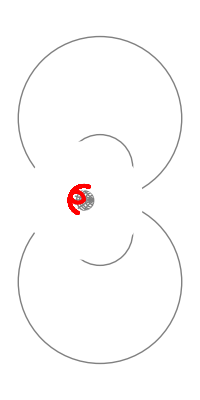

0.743369+(0.743957+1.48733 (-0.999605-14.6422 (0.0000337735+2 δ)))/(1+271246. (0.0000337735+2 δ)^2)

```mathematica
pl=ListPlot[Table[{S11RE[[a]],S11IM[[a]]},{a,1,Length[f]}],PlotStyle->{Red,Thick},PlotRange->All,AspectRatio->Automatic, AxesOrigin->{0,0}];

R1={5,10,20,30,40,60,100,300,500};
X1={10,-10,100,-100,-50,50,-25,25};
chart=Graphics[{Circle[{0,0}],Gray,Table[Circle[{1-1/(1+R1[[a]]/Z0),0},1/(1+R1[[a]]/Z0)],{a,1,Length[R1]}],Table[Circle[{1,Z0/X1[[a]]},Abs[Z0/X1[[a]]]],{a,1,Length[X1]}],Line[{{-1,0},{1,0}}],White,Thickness[0.45],Circle[{0,0},1.5]},PlotRange->1.1];
Show[chart,pl]
model
```

ⅇ^(2 Im[γ]) Abs[0.862189+(0.86253 ⅇ^(ⅈ γ))/(1+(0.+1041.63 ⅈ) δ)]^2

{γ→2.46345}

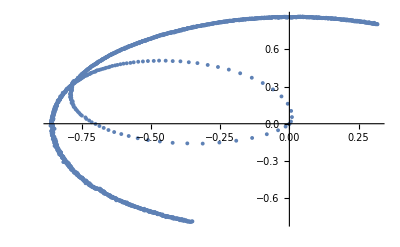

Abs[0.862189-(0.671685-0.541107 ⅈ)/(1+(0.+1041.63 ⅈ) δ)]^2

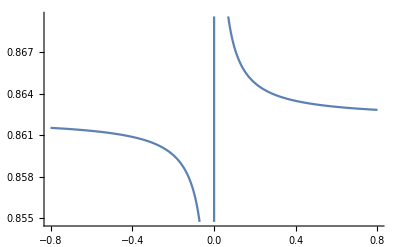

```mathematica
Γ=Abs[Exp[ⅈ (ϕ-γ)](ρ + (d Exp[ⅈγ])/(1+ⅈ QL t))]^2
Smithparam=Table[{S11RE[[x]],S11IM[[x]]},{x,1,Length[S11RE]}];

smithvar=FindFit[Smithparam,Γ,{γ},δ]
ListPlot[Smithparam]
Γ/.smithvar

Plot[(Γ)^(1/2)/.smithvar,{δ,-0.8,0.8}]
```